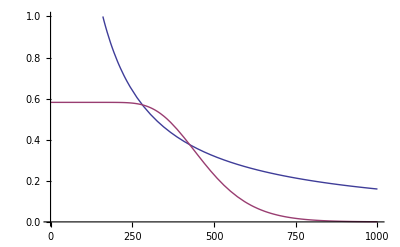

```mathematica
μ=.1;σ=.25;γ=.01;k=550;r=.05;
d[S_]:=1/(σ √T)(Log[S/k]+r T)+σ (√T)/2
z[x_]:=μ/(γ σ^2 x)
T=2;f=z[k];Plot[{z[x] ,2f(1-Erf[d[x]])/2},{x,0,1000},PlotRange-> {0,1}]
```

```mathematica
z[k]
```

0.290909